### Benefit of atomic phase locking

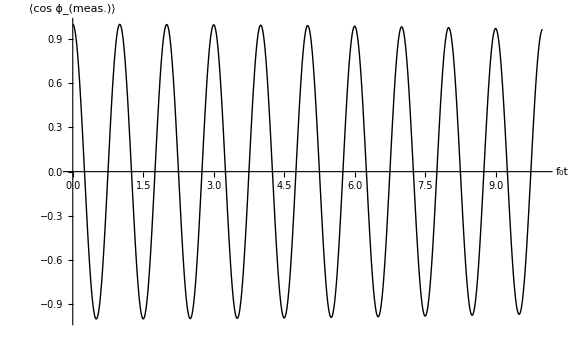

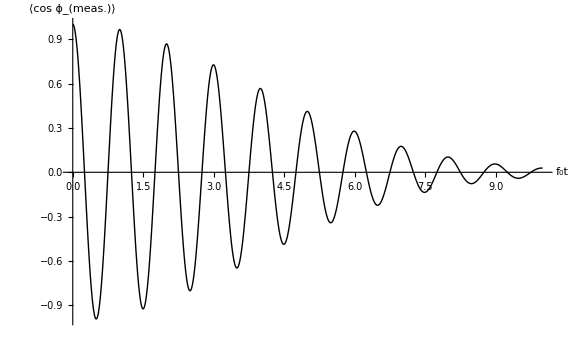

```mathematica
f0=100;
Δf=10/100 f0 ;
Na=100;

f1=f0+Δf;
f2=f0-Δf;

AvgCos[t_]=ⅇ^(-1/2 (2 π  t)^2 (Δf/(2 √(2 Log[2])))^2)Cos[2 π f0 t] ;(*Cos[2 π f0 t];*)

CosAvg[t_]=ⅇ^(-1/2 (2 π  t)^2 (Δf/(√Na 2 √(2 Log[2])))^2) Cos[2 π f0 t];(*Cos[2 π f0 t]*)

Plot[{CosAvg[t/f0]},{t,0,10},PlotRange->{Automatic,Automatic},AxesLabel->{Style["f_0t",Italic,Black,30],Style["⟨cos ϕ_(meas.)⟩",Black,30]},AxesStyle->{{Large,Black},{Large,Black}},ImageSize->Large,PlotStyle->{Thick,Black}]
Plot[{AvgCos[t/f0]},{t,0,10},PlotRange->{Automatic,Automatic},AxesLabel->{Style["f_0t",Italic,Black,30],Style["⟨cos ϕ_(meas.)⟩",Black,30]},AxesStyle->{{Large,Black},{Large,Black}},ImageSize->Large,PlotStyle->{Thick,Black}]
```

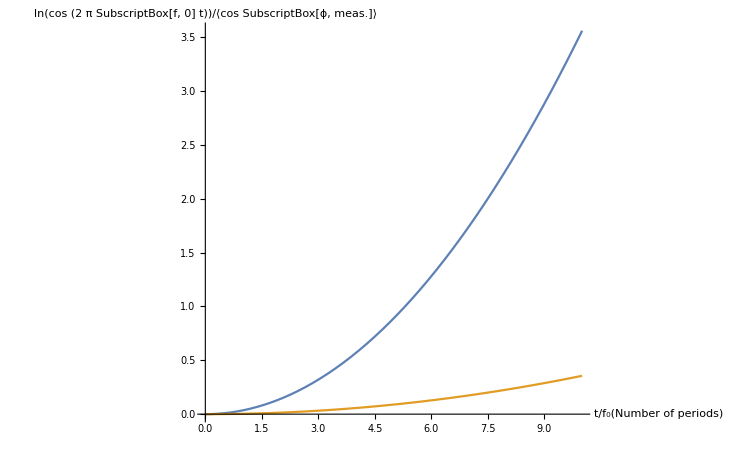

```mathematica
Plot[{1/2 (2 π  t/f0)^2 (Δf/(2 √(2 Log[2])))^2,1/2 (2 π  t/f0)^2 (Δf/(2 √(2 (Na) Log[2])))^2},{t,0,10},PlotRange->{Automatic,Automatic},AxesLabel->{"t/f_0(Number of periods)","ln(cos (2 π SubscriptBox[f, 0] t))/⟨cos SubscriptBox[ϕ, meas.]⟩"},AxesStyle->Large]
```

```mathematica
Simplify[∫_(-∞)^∞ 1/(√(2 π)σ)ⅇ^(-y^2/(2 σ^2))Cos[2π t(f0+y)]ⅆy,σ>0]
```

ⅇ^(-2 π^2 t^2 σ^2) Cos[2 f0 π t]

```mathematica
Simplify[∫_(-∞)^∞ 1/(√(2 π)σ)ⅇ^(-y^2/(2 σ^2))1ⅆy,σ>0]
```

1

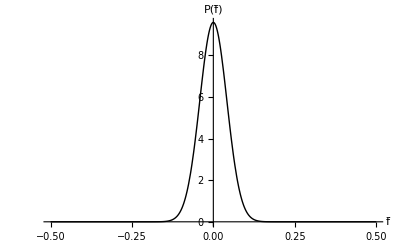

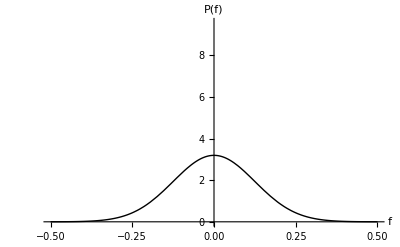

```mathematica
NMAX=9;
Plot[1/(√(2 π)(0.025 5/(√NMAX)))ⅇ^(-(y)^2/(2 (0.025 5/(√NMAX))^2)),{y,-0.5,0.5},PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{Style[f̄,Black],Style["P(f̄)",Italic,Black]},AxesStyle->Large,PlotRange->{-0.01,1/(√(2 π)(0.025 5/(√NMAX)))}]
NMA=1;
Plot[1/(√(2 π)(0.025 5/(√NMA)))ⅇ^(-(y)^2/(2 (0.025 5/(√NMA))^2)),{y,-0.5,0.5},PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{Style[f,Black],Style["P(f)",Italic,Black]},AxesStyle->Large,PlotRange->{-0.01,1/(√(2 π)(0.025 5/(√NMAX)))}]
```